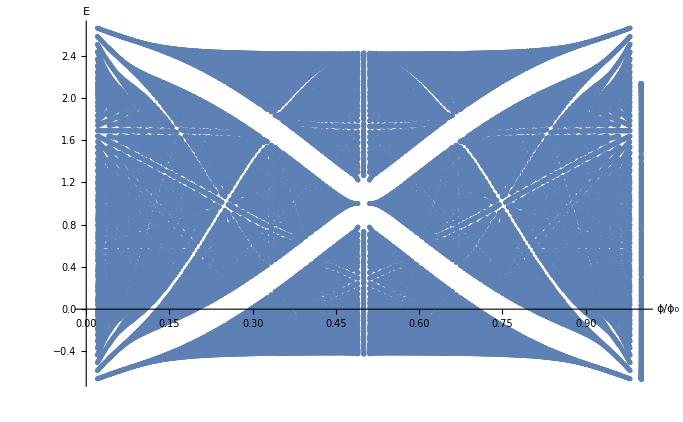

```mathematica
(*The hofstatder butterfly*)
E0=1;
tx=0.7;
ty=0.3;
kx=1;
ky=0.5;
H[q_,phi_]:=Table[(E0-ty*Cos[ky+i*2*Pi*phi])*KroneckerDelta[i,j]
+(-tx*Exp[-I*kx])*KroneckerDelta[i,j-1]
+(-tx*Exp[I*kx])*KroneckerDelta[i,j+1]
+(-tx*Exp[-I*kx*(q+1)])*KroneckerDelta[i,1]*KroneckerDelta[j,q]
+(-tx*Exp[I*kx*(q+1)])*KroneckerDelta[i,q]*KroneckerDelta[j,1]
,{i,1,q},{j,1,q}]
ListPlot[Flatten[Table[Map[{p/q,#}&,Eigenvalues[N[H[q,p/q]]]],{q,1,50},{p,1,q}],2],PlotStyle->PointSize[0.005],AxesLabel->{"ϕ/ϕ_0","E"}]
```